```mathematica
Clear["Global`*"];
```

```mathematica
(*NND fitting formular*) 
ξsb[ξb_?NumericQ]:=Gamma[ξb+1/2]/Gamma[ξb];
(*pp[s_,ξb_]:=(ξb Gamma[3/2+ξb] HypergeometricU[1+ξb,1/2,(s^2 Gamma[ξb]^2)/(4 Gamma[1/2+ξb]^2)])/(√π ξsb[ξb]^2);*)
```

```mathematica
pp[s_,ξb_]:=(2^(-1-2 ξb) Gamma[ξb] Gamma[2+2 ξb] HypergeometricU[1+ξb,1/2,(s^2 Gamma[ξb]^2)/(4 Gamma[1/2+ξb]^2)])/Gamma[1/2+ξb]^2;
```

```mathematica
(* NV fitting formular*)
NV[L_?NumericQ,ξb_?NumericQ]:= L+((ξsb[ξb]/(√ξb))^-2-1) L^2
```

```mathematica
tablemod[{fileNND_String, fileNV_String, fileL_String}]:=Module[{nnd,filename,nlmNND,nv,nlmNV,l}, 
nnd=SetPrecision[Import[fileNND, "Table"],50];
filename=StringDelete[fileNND,"/home/xierr/Desktop/pato_all/pato_new_all/pato_new/Protein_NND_results/"|".txt"];
nlmNND=NonlinearModelFit[nnd/.{x_,y_}:>{x,Log[y]},Log[pp[s,Abs[ξb]]],ξb,s,PrecisionGoal->30,MaxIterations->10000];
nv=Import[fileNV, "Table"];
nlmNV=NonlinearModelFit[nv,NV[L,ξb],ξb,L];
l=Import[fileL];
{filename,ToExpression[l],N[nlmNV["BestFitParameters"][[1,2]]],N[nlmNND["RSquared"]],N[nlmNV["RSquared"]]}]
```

```mathematica
(*plotmod[file_String]:=Module[{nnd}, 
nnd=Import[file, "Table"];
ListPlot[nnd,PlotMarkers->Automatic]]*)
```

```mathematica
filesNND=FileNames["*.txt","/home/xierr/Desktop/pato_all/pato_new_all/pato_new/Protein_NND_results"];
filesNV=FileNames["*.txt","/home/xierr/Desktop/pato_all/pato_new_all/pato_new/Protein_NV_results"];
filesL=FileNames["*.txt","/home/xierr/Desktop/pato_all/pato_new_all/pato_new/Protein_L_results"];
```

```mathematica
CloseKernels[];LaunchKernels[4];
DistributeDefinitions[tablemod,filesNND,filesNV,filesL];
```

```mathematica
TableForm[ParallelMap[tablemod[#]&,Transpose[{filesNND,filesNV,filesL}]]/.{x_Real:>NumberForm[x,{15,4}]},TableHeadings->{None,{"Sequence","⟨L⟩","λ","R_NND^2","R_NV^2"}}]
```

Sequence | ⟨L⟩ | λ | R_NND^2 | R_NV^2
A2ASS6 | 9.7640 | 2.4410 | 0.9828 | 0.9984
A5ISW6 | 6.4609 | 6.1821 | 0.9722 | 0.9977
A6QGY5 | 6.6798 | 4.2482 | 0.9625 | 0.9954
A6U1Q5 | 6.4609 | 6.1821 | 0.9722 | 0.9977
A8Z414 | 6.4755 | 5.7239 | 0.9719 | 0.9985
C6KTB7 | 5.2360 | 61.0471 | 0.9617 | 0.8978
C6KTD2 | 3.9227 | 20.9135 | 0.9740 | 0.8683
G4SLH0 | 6.8232 | 4.0993 | 0.9841 | 0.9951
O01761 | 9.3111 | 8.0235 | 0.9560 | 0.9911
P0C6W0 | 8.9194 | 49.2152 | 0.9608 | 0.9800
P0C6W1 | 9.4603 | 81.6309 | 0.9582 | 0.9913
P0C6W2 | 9.3824 | 80.5407 | 0.9510 | 0.9312
P0C6W3 | 9.5744 | 125.1087 | 0.9604 | 0.9858
P0C6W4 | 9.5538 | 267.8640 | 0.9628 | 0.9724
P0C6W5 | 8.9798 | 55.3474 | 0.9628 | 0.9850
P0C6W6 | 9.4807 | 100.4821 | 0.9527 | 0.9263
P0C6W7 | 8.9816 | 844.0069 | 0.9713 | 0.9787
P0C6X1 | 9.0581 | 37.8563 | 0.9544 | 0.9907
P0C6X2 | 8.9428 | 138.5793 | 0.9677 | 0.9797
P0C6X5 | 8.9408 | 37.9580 | 0.9461 | 0.9844
P0C6X7 | 9.4993 | 82.9880 | 0.9519 | 0.9448
P0C6X9 | 8.5523 | 128.1919 | 0.9745 | 0.9896
P0C6Y5 | 9.9540 | 3048.6813 | 0.9302 | 0.9396
P20929 | 6.9734 | 51.3331 | 0.9570 | 0.9860
Q008X6 | 7.7116 | 14.4602 | 0.9575 | 0.9859
Q03001 | 7.9244 | 180.4337 | 0.9533 | 0.9656
Q09165 | 7.8363 | 66.2442 | 0.9440 | 0.8309
Q09221 | 7.5635 | 28.0167 | 0.9580 | 0.9339
Q18DN4 | 6.2448 | 10.4502 | 0.9694 | 0.9880
Q18SQ001 | 6.2448 | 10.4502 | 0.9694 | 0.9880
Q23551 | 10.8212 | 5.2961 | 0.9263 | 0.9844
Q2FYJ6 | 6.7026 | 5.4466 | 0.9695 | 0.9979
Q54CU4 | 9.8690 | 19.3091 | 0.9278 | 0.9677
Q54QG5 | 7.3357 | 2661.3817 | 0.9588 | 0.6893
Q555C6 | 6.9174 | 12.0236 | 0.9155 | 0.8391
Q5CZC0 | 7.7560 | 4213.3978 | 0.9532 | 0.8868
Q5HFY8 | 6.4825 | 5.7351 | 0.9720 | 0.9985
Q5VST9 | 8.6553 | 82.1596 | 0.9739 | 0.9818
Q6GGX3 | 6.4316 | 6.8655 | 0.9681 | 0.9978
Q6PZE0 | 3.4592 | 6.2516 | 0.9408 | 0.9813
Q6ZWQ0 | 6.3742 | 2037.2259 | 0.9752 | 0.9483
Q7Z5P9 | 4.0720 | 3.6984 | 0.9600 | 0.9984
Q869L3 | 8.2019 | 48.9964 | 0.9141 | 0.6945
Q8CP76 | 6.9467 | 2271.1392 | 0.9822 | 0.5307
Q8I3Z1 | 4.0553 | 28.2205 | 0.9755 | 0.8948
Q8NF91 | 6.6513 | 1697.3999 | 0.9798 | 0.8256
Q8NWQ6 | 6.4920 | 5.6685 | 0.9680 | 0.9982
Q8R0W0 | 7.4844 | 156.1764 | 0.8718 | 0.9697
Q8VHN7 | 9.5597 | 1633.6197 | 0.9606 | 0.9556
Q8WXH0 | 6.7007 | 1835.9375 | 0.9612 | 0.6057
Q8WXI7 | 4.4777 | 13.1243 | 0.9783 | 0.9613
Q8WZ42 | 9.4678 | 2.4147 | 0.9865 | 0.9997
Q91ZU6 | 7.8091 | 34.0320 | 0.9527 | 0.9782
Q9I7U4 | 5.6634 | 3.3648 | 0.9797 | 0.9959
Q9QXZ0 | 7.3849 | 1047.2609 | 0.9665 | 0.9002
Q9UPN3 | 7.4821 | 3973.1601 | 0.9463 | 0.8159
W6RTA4 | 6.9139 | 1514.8847 | 0.9636 | 0.9818

```mathematica
(*OutputForm[TableForm[Map[tablemod[#]&,Transpose[{filesNND,filesNV,filesL}]]/.{x_Real:>NumberForm[x,{15,4}]},TableHeadings->{None,{"Sequence","⟨L⟩","β","f_NV","ξ_NV","R_NND^2","R_NV^2"}}]]>>"test"*)
```

```mathematica
(*Export["/home/xierr/Desktop/tableIII.dat",Map[tablemod[#]&,Transpose[{filesNND,filesNV,filesL}]]/.{x_Real:>NumberForm[x,{15,4}]}];*)
```

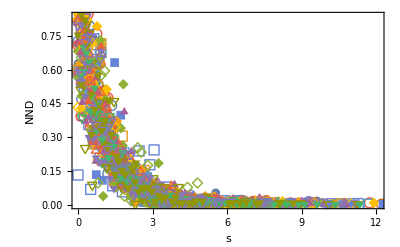

```mathematica
plotNND=ListPlot[Import[#,"Data"]&/@filesNND,PlotMarkers->Automatic, Frame->True,FrameLabel->{Style["s",FontFamily->"Times",Italic,15],Style["NND",FontFamily->"Times",Italic,15]}]
```

```mathematica
nnd1=Import["13630-8.txt","Table"];
nlmNND1=NonlinearModelFit[nnd1,p[s,β],β,s];
```

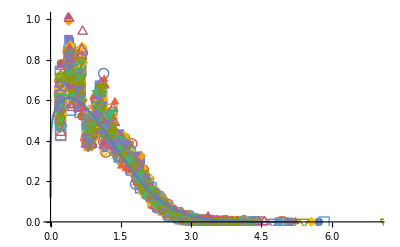

```mathematica
Show[plotNND,Plot[Normal[nlmNND1],{s,0,5},PlotRange->All]]
```

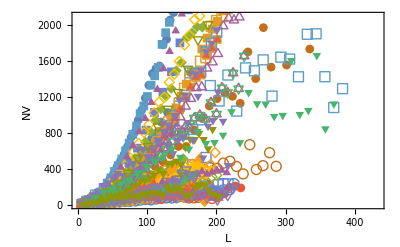

```mathematica
plotNV=ListPlot[Import[#,"Data"]&/@filesNV,PlotMarkers->Automatic,Frame->True,FrameLabel->{Style["L",FontFamily->"Times",Italic,15],Style["NV",FontFamily->"Times",Italic,15]}]
```

```mathematica
nv1=Import["13630_NV.txt","Table"];
nlmNV1=NonlinearModelFit[nv1,NV[L,ξb,f],{ξb,f},L];
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

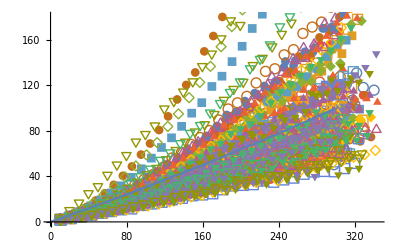

```mathematica
Show[plotNV,Plot[Normal[nlmNV1],{L,0,300},PlotRange->All]]
```